```mathematica
SetDirectory[NotebookDirectory[]];
a=Import["y_test2_1.csv","Data"];
b=Import["y_hat2_1.csv","Data"];
Dimensions[a]
Dimensions[b]
```

{400,4}

{400,4}

0.633962810039520264

0.0000119399001050624065

0.042000626217063655

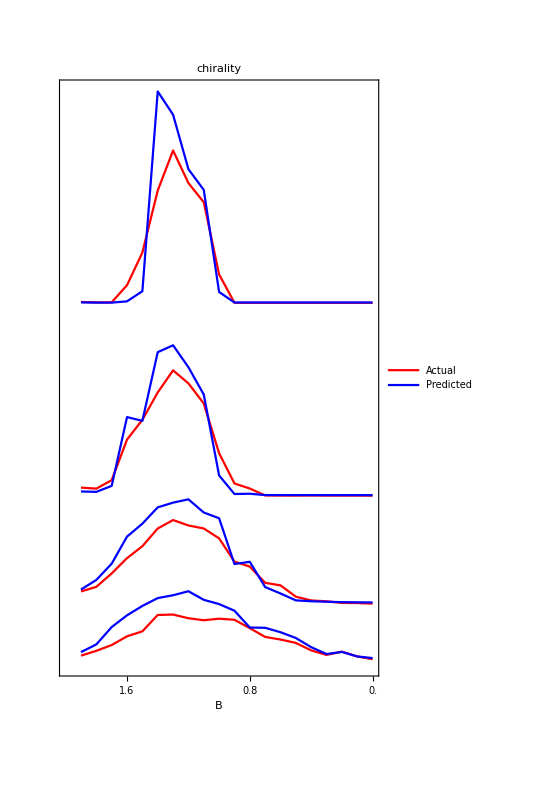

```mathematica
a1=ArrayReshape[a[[All,1]],{20,20}];
Max[a1]
Min[a1]
b1=ArrayReshape[b[[All,1]],{20,20}];
sum=0;
For [i=1,i≤20,i++,
For[j=0,j≤20,j++,
sum=sum+Abs[b1[[i,j]]-a1[[i,j]]]]];
sum/400
ListPlot[{a1[[All,5]],b1[[All,5]],0.25+a1[[All,10]],0.25+b1[[All,10]],0.7+a1[[All,15]],0.7+b1[[All,15]],1.5+a1[[All,20]],1.5+b1[[All,20]]},Frame->True,AspectRatio->2,FrameLabel->{Style[B,FontSize->16]},PlotLabel->Style["chirality",FontSize->20],Joined->True,FrameTicks->{xtick,None},PlotStyle->{Red,Blue,Red,Blue,Red,Blue,Red,Blue},FrameTicksStyle->Directive[Black,12],PlotLabel->{"T=2.0",None,"T=1.5",None,"T=0.5",None,"T=0.1",None},PlotLegends->{"Actual","Predicted"}]
```

0.991125285625457764

0.00431774044409394264

0.023762868102639914

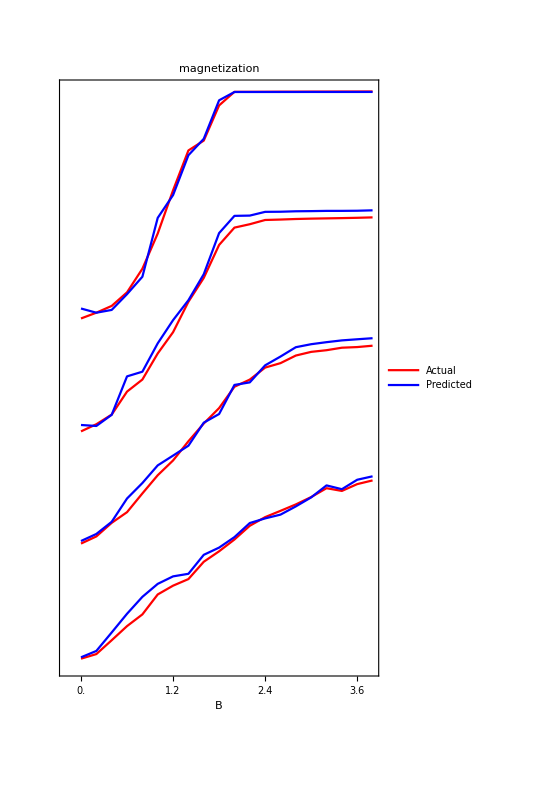

```mathematica
a2=ArrayReshape[a[[All,2]],{20,20}];
Max[a2]
Min[a2]
b2=ArrayReshape[b[[All,2]],{20,20}];
sum=0;
For [i=1,i≤20,i++,
For[j=0,j≤20,j++,
sum=sum+Abs[b2[[i,j]]-a2[[i,j]]]]];
sum/400
xtick=Table[{i,(i-1)/5.0},{i,1,30,3}];
ListPlot[{a2[[All,5]],b2[[All,5]],0.5+a2[[All,10]],0.5+b2[[All,10]],1.0+a2[[All,15]],1+b2[[All,15]],1.5+a2[[All,20]],1.5+b2[[All,20]]},Frame->True,AspectRatio->2,FrameLabel->{Style[B,FontSize->16]},PlotLabel->Style["magnetization",FontSize->20],Joined->True,FrameTicks->{xtick,None},PlotStyle->{Red,Blue,Red,Blue,Red,Blue,Red,Blue},FrameTicksStyle->Directive[Black,12],PlotLabel->{"T=2.0",None,"T=1.5",None,"T=0.5",None,"T=0.1",None},PlotLegends->{"Actual","Predicted"}]
```

0.949999749660491943

0.

0.152241

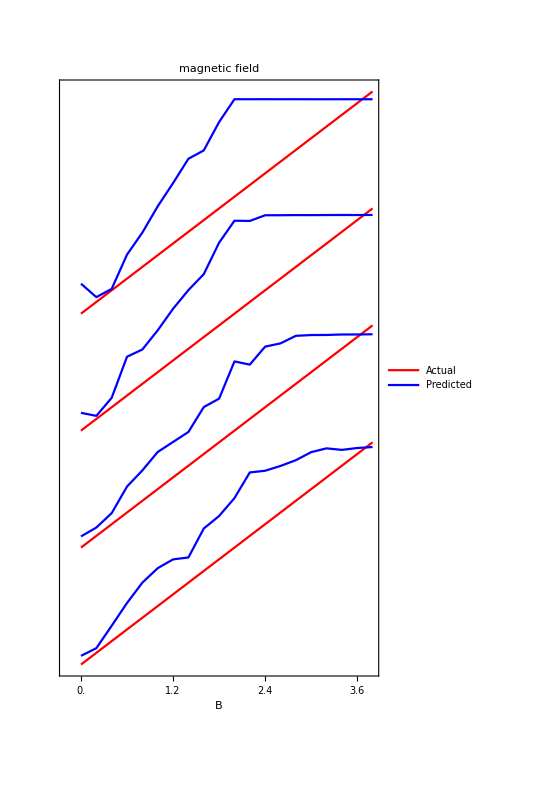

```mathematica
a3=ArrayReshape[a[[All,3]],{20,20}];
Max[a3]
Min[a3]
b3=ArrayReshape[b[[All,3]],{20,20}];
sum=0;
For [i=1,i≤20,i++,
For[j=0,j≤20,j++,
sum=sum+Abs[b3[[i,j]]-a3[[i,j]]]]];
sum/400
xtick=Table[{i,(i-1)/5.0},{i,1,30,3}];
ListPlot[{a3[[All,5]],b3[[All,5]],0.5+a3[[All,10]],0.5+b3[[All,10]],1+a3[[All,15]],1+b3[[All,15]],1.5+a3[[All,20]],1.5+b3[[All,20]]},Frame->True,AspectRatio->2,FrameLabel->{Style[B,FontSize->16]},PlotLabel->Style["magnetic field",FontSize->20],Joined->True,FrameTicks->{xtick,None},PlotStyle->{Red,Blue,Red,Blue,Red,Blue,Red,Blue},FrameTicksStyle->Directive[Black,12],PlotLabel->{"T=2.0",None,"T=1.5",None,"T=0.5",None,"T=0.1",None},PlotLegends->{"Actual","Predicted"}]
```

1.

0.0500000156462192535

0.10017456640489399

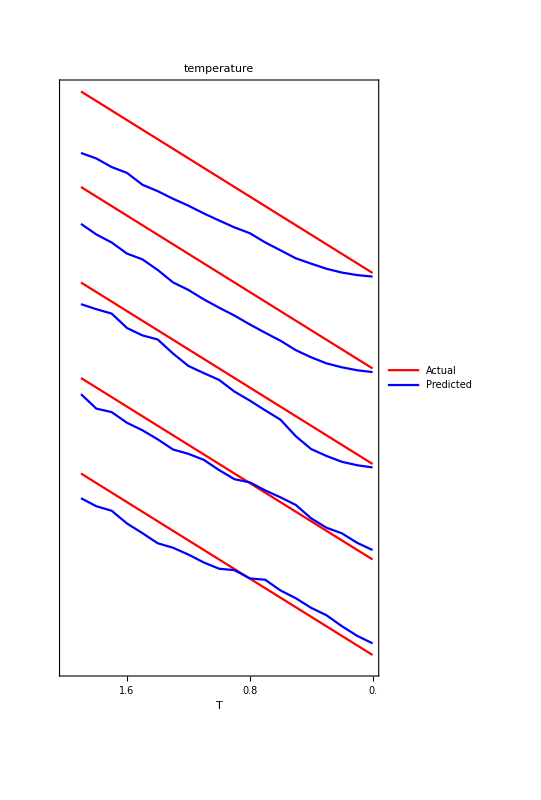

```mathematica
a4=ArrayReshape[a[[All,4]],{20,20}];
Max[a4]
Min[a4]
b4=ArrayReshape[b[[All,4]],{20,20}];
sum=0;
For [i=1,i≤20,i++,
For[j=0,j≤20,j++,
sum=sum+Abs[b4[[i,j]]-a4[[i,j]]]]];
sum/400
xtick=Table[{i,(20-i)/10.0},{i,20,0,-4}];
ListPlot[{a4[[1,All]],b4[[1,All]],0.5+a4[[6,All]],0.5+b4[[6,All]],1+a4[[11,All]],1.0+b4[[11,All]],1.5+a4[[16,All]],1.5+b4[[16,All]],2+a4[[20,All]],2+b4[[20,All]]},Frame->True,AspectRatio->2,FrameLabel->{Style[T,FontSize->16]},PlotLabel->Style["temperature",FontSize->20],Joined->True,FrameTicks->{xtick,None},PlotStyle->{Red,Blue,Red,Blue,Red,Blue,Red,Blue},FrameTicksStyle->Directive[Black,12],PlotLabel->{"T=2.0",None,"T=1.5",None,"T=0.5",None,"T=0.1",None},PlotLegends->{"Actual","Predicted"}]
```